```mathematica
P1=Import["P1.txt","Table"];
P2=Import["P2.txt","Table"];
```

```mathematica
Clear[Vp];
μ=50;
nn=49;
wc=μ/(nn+1);
(*Ez=(3/4)*wc;*)
{Ez,me,α,β}={0.5*wc,1,0.5,1};
data={};
(*x1=(2-(1-α)*Vp)*4*α*Vp/(((1-α)*Vp)*(2-(1+3*α)))/.Vp->0.01
x2=(2-(1-α)*Vp)*4*α*Vp/(((1-α)*Vp)*(2-(1+3*α)))/.Vp->π*)
```

```mathematica
For[Vp=0.01,Vp≤π,Vp+=0.05,
{
l=1/Sqrt[me*wc];
kf[n_,s_]:=Re[Sqrt[2*me*(μ-((n+1/2)*wc-Sign[s]*Ez/2))]];
(*sn[n_,m_]:=(-1/Pi)*(1/l)*(kf[m,-1]*P1[[n+1,m+1]]-kf[m,+1]*P1[[n+2,m+1]]);*)
sn[n_,m_]:=(-1/π)*(1/l)*(kf[m,-1]*((β+α)*P1[[n+1,m+1]]-2*α*P1[[n+1,m+1]])+kf[m,+1]*(2*α*P1[[n+1,m+1]]-(β+α)*P1[[n+1,m+1]]));
s[n_]:=Sum[sn[n,m],{m,0,nn+1}];
sm[n_,m_]:=Piecewise[{{s[n],n==m}},0];
smatrix=Table[sm[n,m],{n,0,nn},{m,0,nn}];
km[n_,m_]:=Piecewise[{{(1/Pi)*(kf[n,-1]-kf[n,+1]),n==m}},0];kmatrix=Table[km[n,m],{n,0,nn},{m,0,nn}];
vmatrix=Table[(1/l)*(β-α)*P1[[n+1,m+1]],{n,0,nn},{m,0,nn}];
M=-kmatrix.vmatrix-smatrix;
For[i=0,i≤nn,i++,
{mm=Eigenvalues[M][[i+1]];
ω=Vp*mm+(Ez);
AppendTo[data,{Vp*me/π,ω/wc}]}];
}]
```

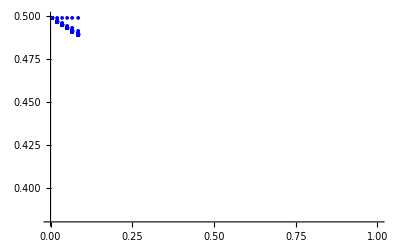

```mathematica
f1=ListPlot[data,PlotStyle->Blue,PlotRange->{{0,1},Automatic},PlotLegends->SwatchLegend[{Blue},{"ω"}],AxesLabel->{"V_0m_e/π","ω/ω_c"},PlotMarkers->{Automatic,5}]
```

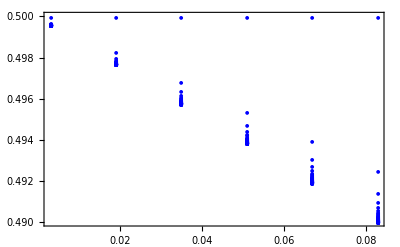

```mathematica
x={0.51,0.38};y=Table[-10+.1*i,{i,0,200}];
f1=ListPlot[data,PlotStyle->Blue,PlotRange->{{0,1},x},Frame->{True,True,True,True},FrameStyle->Directive[Thickness[0.006],16],GridLines->{None,None},FrameLabel->{Style["V̄ν",Large],Style["ω/ω_c",Large]},LabelStyle->Directive[12,FontFamily->"Times"],FrameTicks->{Automatic,y,None,None},PlotMarkers->{Automatic,5}]
```

```mathematica
x={0.52,0.38};y=Table[-10+.1*i,{i,0,200}];
f1=ListPlot[data,PlotStyle->Blue,PlotRange->{{0,1},x},Frame->{True,True,True,True},FrameLabel->{"V_0/π","ω/ω_c",None,None},FrameTicks->{Automatic,y,None,None},PlotMarkers->{Automatic,5}]
```

-Graphics-

```mathematica
Export["n(up)&n(down)_Vp=1_Vs=0-5Vp_Ez=0-5wc_nn=49.eps",Show[f1]];
```

```mathematica
Export["n(up)&n(down)_Vp=1_Vs=0-5Vp_Ez=0-5wc_nn=49.eps",Show[f1,Frame->{True,True,True,True},FrameLabel->{None,None,None,None},LabelStyle->Directive[Black,20],FrameTicks->{Automatic,y,None,None}],ImageResolution->600,ImageSize->400];
Show[f1]
```

-Graphics-

```mathematica
f2=Plot[-(1/wc)*(Ez+Ez*q*(β-α)/(2*(2-(β-α)*q))-Sqrt[Ez^2*((β-α)*q)^2/(4*(2-(β-α)*q)^2)+wc^2*(2-(β-α)*q)/(2-(β+3*α)*q)]),{q,0,1},PlotRange->x,PlotStyle->{Thickness[0.008],Red},Frame->{True,True,True,True},FrameLabel->{"V_0/π","ω/ω_c",None,None},FrameTicks->{Automatic,Automatic,None,None}]
```

-Graphics-

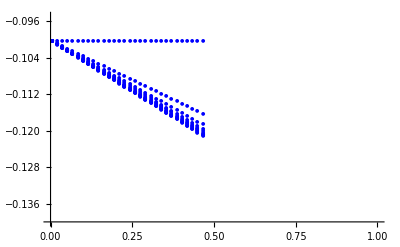

```mathematica
Show[f1,f2]
```

```mathematica
Export["Vs=0_Ez=0-9wc_nn=9.jpg",Show[f1,f2],ImageResolution->600,ImageSize->1000]
```

Vs=0_Ez=0.9wc_nn=9.jpg

```mathematica
Eigenvalues[M]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}